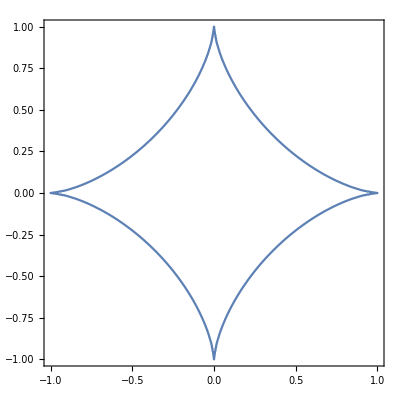

```mathematica
ContourPlot[Abs[x]^(2/3) + Abs[y]^(2/3) == 1,{x,-1,1},{y,-1,1}]
```

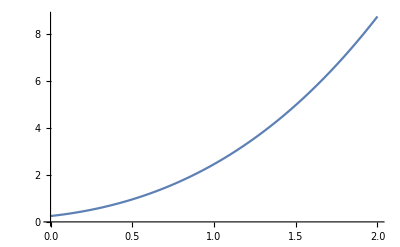

```mathematica
Plot[x^3/3+x^2+x+1/(4x+4),{x,0,2}]
```

```mathematica
a = 0
```

0

```mathematica
b = 2
```

2

```mathematica
n = 1
```

1

```mathematica
delta[a_,b_,n_] := (b-a)/n
```

```mathematica
x[a_,b_,n_,i_] := a + i*delta[a,b,n]
```

```mathematica
y[x_] := x^3/3+x^2+x+1/(4*x+4)
```

```mathematica
N[Sum[(delta[a,b,n]^2+y[x[a,b,n,i]]^2)^(1/2),{i,0,n-1}]]
```

2.01556

```mathematica
y[2]
```

35/4

```mathematica
N[(35/4)^2+2^2]
```

80.5625